# What is Chirality? How do we encounter it in our everyday, and not-so-everyday lives?

Cody Trevillian, Jun. 29, 2019

## I’m not sure, where do you see chirality in your daily life?

Look at your mirror-reflection:

```mathematica
ImageCapture[]
```

## Okay, easy! But...what does this have to do with chirality?

Everything! But, you have a point there. We can start simple and small. Have you ever seen a "rose chafer"?

```mathematica
Grid[{{Framed@Entity["Species", "Species:CetoniaAurata"][EntityProperty["Species", "Image"]], Dataset[EntityValue[Entity["Species", "Species:CetoniaAurata"], {EntityProperty["Species", "Kingdom"], EntityProperty["Species", "Phylum"], EntityProperty["Species", "Class"], EntityProperty["Species", "Order"], EntityProperty["Species", "Family"], EntityProperty["Species", "Genus"], EntityProperty["Species", "Species"]}, "PropertyAssociation"]]}}]
```

-Graphics- | Dataset[<>]

Well, maybe not if you live in the USA!

```mathematica
TextSentences[WikipediaData[Entity["Species","Species:CetoniaAurata"]]]⟦12;;13⟧
```

{Rose chafers are found in southern and central Europe and in the southern part of the United Kingdom, where they sometimes seem to be very localized.,They can also be found in South East Asia, in the countryside and outlying islands of Hong Kong.}

So if you haven’t seen one before, and you want more information, try looking with WolframAlpha:

WolframAlphaQueryResults

## This is all well and good, but why are we talking about a beetle?

Oh, right! So, check it out, the coloration of this awesome insect is chiral; the green-metallic coloration is due to a reflection of left-polarized light! Don’t believe me? Read it here:

```mathematica
TextSentences[WikipediaData[Entity["Species","Species:CetoniaAurata"]]]⟦23;;30⟧
```

{== Coloration ==,The metallic green coloration of the beetle is created structurally, caused by the reflection of mostly circularly polarised light;,like other scarabs this is left circularly polarised.,When viewed through a right circular polariser, the beetle appears to be colorless.,There are also different colors besides the common green;,there is also copper, grey and black.,A lot of specimens have white speckles while some have very few or none at all.,It has been described as a left-hand narrow-band elliptical polarizer.}

## Okay, I’m a little more lost than before, how does left-polarized light apply to chirality?

So, chirality is based on mirror-symmetry, if the mirror-reflection has no way of being reoriented through rotations and translations, then it is chiral, otherwise, it is achiral! This is just like the left- and right-handed polarizations of light that we see every day!

## I don’t quite understand, can you show me an example without light?

The following is a "trefoil", try rotating the left image to match it up with the right one:

```mathematica
Grid[{{KnotData["Trefoil"], ImageReflect@Rasterize@KnotData["Trefoil"]}}]
```

-Graphics3D- | -Graphics-

So, you can see that this knot is chiral! Cool, huh?

## Okay...but I’ve never seen something like that before, can you give me a more...relatable example?

## Am “I” Chiral?

Well, no. “I”is not chiral, but “You” are!

```mathematica
Grid[{{, ImageReflect[,Left]}, {ImageReflect[], ImageReflect[ImageReflect@,Left]}},Spacings->{0,-8}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{, ImageReflect[,Left]}, {ImageReflect[], ImageReflect[ImageReflect@,Left]}},Spacings->{0,-8}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

## Alright, you made more art, but what does this mean to me?

Look at your hands. Make one look like the other, try it:

```mathematica
Grid[{{AnatomyPlot3D[Entity["AnatomicalStructure","LeftHand"],AnatomySkinStyle->Directive[CMYKColor[0,0.145,0.940,0.003,0.85]],ViewAngle->Automatic,ViewCenter->{0.5,0.5,0.5},ViewMatrix->Automatic,ViewPoint->{-0.018236850028756295,1.7956499231694103,-0.6207324469710918},ViewProjection->Automatic,ViewRange->All,ViewVector->Automatic,ViewVertical->{0.22730091896746454,-0.4272616251612543,-0.8750895930709666}], AnatomyPlot3D[Entity["AnatomicalStructure","RightHand"],AnatomySkinStyle->Directive[CMYKColor[0,0.145,0.940,0.003,0.85]],ViewAngle->Automatic,ViewCenter->{0.5,0.5,0.5},ViewMatrix->Automatic,ViewPoint->{0.1390766345555284,-1.8693118008211327,0.3103724875557765},ViewProjection->Automatic,ViewRange->All,ViewVector->Automatic,ViewVertical->{-0.15256353118435254,-0.23710148253086327,-0.9594306936586029}]}}]
```

-Graphics3D- | -Graphics3D-

That’s chirality: Your hands are mirror-reflections of each other--you can’t superimpose one on the other, no matter how much you try!

## Wow! So, who discovered chirality? Louis Chiral?

Not quite! But close:

```mathematica
Grid[{{Entity["Person","LouisPasteur::d7488"][EntityProperty["Person","Image"]], Dataset[EntityValue[Entity["Person","LouisPasteur::d7488"],{EntityProperty["Person","FullName"],EntityProperty["Person","BirthDate"],EntityProperty["Person","BirthPlace"],EntityProperty["Person","DeathDate"],EntityProperty["Person","DeathPlace"]},"PropertyAssociation"]]}}]
```

-Graphics- | Dataset[<>]

Here’s some more information from WolframAlpha:

WolframAlphaQueryParseResults

It is surprising that the only contribution deemed worthy enough of Pasteur’s namesake were of his work on "pasteurization""  ""(""1864"")" !

## We are homo-chiral, exhibiting a uniformity of chirality: our proteins are exclusively left-handed, and our RNA and DNA are comprised of right-handed sugars. Let’s look at some chiral structures we enjoy every day in our lives:

### Try to reorient the left DNA strand like the right one, like the hands from before

```mathematica
Grid[ {
  {Graphics3D[{{{RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.09888308262251286, -0.014904226617617443, -0.9523809523809523}, {0., 0., -0.9523809523809523}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.09009688679024191, -0.04338837391175582, -0.8571428571428571}, {0., 0., -0.8571428571428571}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.07330518718298264, -0.06801727377709194, -0.7619047619047619}, {0., 0., -0.7619047619047619}}, 0.005000000000000001]}, {RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.05, -0.08660254037844387, -0.6666666666666666}, {0., 0., -0.6666666666666666}}, 0.005000000000000001]}, {RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.02225209339563144, -0.09749279121818237, -0.5714285714285714}, {0., 0., -0.5714285714285714}}, 0.005000000000000001]}, {RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{0.007473009358642424, -0.09972037971811802, -0.47619047619047616}, {0., 0., -0.47619047619047616}}, 0.005000000000000001]}, {RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{0.0365341024366395, -0.09308737486442042, -0.38095238095238093}, {0., 0., -0.38095238095238093}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{0.06234898018587335, -0.07818314824680299, -0.2857142857142857}, {0., 0., -0.2857142857142857}}, 0.005000000000000001]}, {RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{0.08262387743159949, -0.0563320058063622, -0.19047619047619047}, {0., 0., -0.19047619047619047}}, 0.005000000000000001]}, {RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{0.09555728057861408, -0.029475517441090417, -0.09523809523809523}, {0., 0., -0.09523809523809523}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{0.1, 0., 0.}, {0., 0., 0.}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{0.09555728057861408, 0.029475517441090417, 0.09523809523809523}, {0., 0., 0.09523809523809523}}, 0.005000000000000001]}, {RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{0.08262387743159949, 0.0563320058063622, 0.19047619047619047}, {0., 0., 0.19047619047619047}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{0.06234898018587335, 0.07818314824680299, 0.2857142857142857}, {0., 0., 0.2857142857142857}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{0.0365341024366395, 0.09308737486442042, 0.38095238095238093}, {0., 0., 0.38095238095238093}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{0.007473009358642424, 0.09972037971811802, 0.47619047619047616}, {0., 0., 0.47619047619047616}}, 0.005000000000000001]}, {RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.02225209339563144, 0.09749279121818237, 0.5714285714285714}, {0., 0., 0.5714285714285714}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{-0.05, 0.08660254037844387, 0.6666666666666666}, {0., 0., 0.6666666666666666}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.07330518718298264, 0.06801727377709194, 0.7619047619047619}, {0., 0., 0.7619047619047619}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{-0.09009688679024191, 0.04338837391175582, 0.8571428571428571}, {0., 0., 0.8571428571428571}}, 0.005000000000000001]}, {RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.09888308262251286, 0.014904226617617443, 0.9523809523809523}, {0., 0., 0.9523809523809523}}, 0.005000000000000001]}}, {{RGBColor[0, 4/9, 0], Tube[{{0.1, 0., -1.}, {0.09555728057861408, 0.029475517441090417, -0.9047619047619048}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{0.09555728057861408, 0.029475517441090417, -0.9047619047619048}, {0.08262387743159949, 0.0563320058063622, -0.8095238095238095}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{0.08262387743159949, 0.0563320058063622, -0.8095238095238095}, {0.06234898018587335, 0.07818314824680299, -0.7142857142857143}}, 0.010000000000000002]}, {RGBColor[2/3, 0, 0], Tube[{{0.06234898018587335, 0.07818314824680299, -0.7142857142857143}, {0.0365341024366395, 0.09308737486442042, -0.6190476190476191}}, 0.010000000000000002]}, {RGBColor[2/3, 0, 0], Tube[{{0.0365341024366395, 0.09308737486442042, -0.6190476190476191}, {0.007473009358642424, 0.09972037971811802, -0.5238095238095238}}, 0.010000000000000002]}, {RGBColor[2/3, 0, 0], Tube[{{0.007473009358642424, 0.09972037971811802, -0.5238095238095238}, {-0.02225209339563144, 0.09749279121818237, -0.42857142857142855}}, 0.010000000000000002]}, {RGBColor[0, 4/9, 0], Tube[{{-0.02225209339563144, 0.09749279121818237, -0.42857142857142855}, {-0.05, 0.08660254037844387, -0.3333333333333333}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{-0.05, 0.08660254037844387, -0.3333333333333333}, {-0.07330518718298264, 0.06801727377709194, -0.23809523809523808}}, 0.010000000000000002]}, {RGBColor[0, 4/9, 0], Tube[{{-0.07330518718298264, 0.06801727377709194, -0.23809523809523808}, {-0.09009688679024191, 0.04338837391175582, -0.14285714285714285}}, 0.010000000000000002]}, {RGBColor[0, 4/9, 0], Tube[{{-0.09009688679024191, 0.04338837391175582, -0.14285714285714285}, {-0.09888308262251286, 0.014904226617617443, -0.047619047619047616}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{-0.09888308262251286, 0.014904226617617443, -0.047619047619047616}, {-0.09888308262251286, -0.014904226617617443, 0.047619047619047616}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{-0.09888308262251286, -0.014904226617617443, 0.047619047619047616}, {-0.09009688679024191, -0.04338837391175582, 0.14285714285714285}}, 0.010000000000000002]}, {RGBColor[0, 4/9, 0], Tube[{{-0.09009688679024191, -0.04338837391175582, 0.14285714285714285}, {-0.07330518718298264, -0.06801727377709194, 0.23809523809523808}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{-0.07330518718298264, -0.06801727377709194, 0.23809523809523808}, {-0.05, -0.08660254037844387, 0.3333333333333333}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{-0.05, -0.08660254037844387, 0.3333333333333333}, {-0.02225209339563144, -0.09749279121818237, 0.42857142857142855}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{-0.02225209339563144, -0.09749279121818237, 0.42857142857142855}, {0.007473009358642424, -0.09972037971811802, 0.5238095238095238}}, 0.010000000000000002]}, {RGBColor[0, 4/9, 0], Tube[{{0.007473009358642424, -0.09972037971811802, 0.5238095238095238}, {0.0365341024366395, -0.09308737486442042, 0.6190476190476191}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{0.0365341024366395, -0.09308737486442042, 0.6190476190476191}, {0.06234898018587335, -0.07818314824680299, 0.7142857142857143}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{0.06234898018587335, -0.07818314824680299, 0.7142857142857143}, {0.08262387743159949, -0.0563320058063622, 0.8095238095238095}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{0.08262387743159949, -0.0563320058063622, 0.8095238095238095}, {0.09555728057861408, -0.029475517441090417, 0.9047619047619048}}, 0.010000000000000002]}, {RGBColor[2/3, 0, 0], Tube[{{0.09555728057861408, -0.029475517441090417, 0.9047619047619048}, {0.1, 0., 1.}}, 0.010000000000000002]}}, {{{RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{0.09888308262251286, 0.014904226617617443, -0.9523809523809523}, {0., 0., -0.9523809523809523}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{0.09009688679024191, 0.04338837391175582, -0.8571428571428571}, {0., 0., -0.8571428571428571}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{0.07330518718298264, 0.06801727377709194, -0.7619047619047619}, {0., 0., -0.7619047619047619}}, 0.005000000000000001]}, {RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{0.05, 0.08660254037844387, -0.6666666666666666}, {0., 0., -0.6666666666666666}}, 0.005000000000000001]}, {RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{0.02225209339563144, 0.09749279121818237, -0.5714285714285714}, {0., 0., -0.5714285714285714}}, 0.005000000000000001]}, {RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.007473009358642424, 0.09972037971811802, -0.47619047619047616}, {0., 0., -0.47619047619047616}}, 0.005000000000000001]}, {RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.0365341024366395, 0.09308737486442042, -0.38095238095238093}, {0., 0., -0.38095238095238093}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.06234898018587335, 0.07818314824680299, -0.2857142857142857}, {0., 0., -0.2857142857142857}}, 0.005000000000000001]}, {RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.08262387743159949, 0.0563320058063622, -0.19047619047619047}, {0., 0., -0.19047619047619047}}, 0.005000000000000001]}, {RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.09555728057861408, 0.029475517441090417, -0.09523809523809523}, {0., 0., -0.09523809523809523}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{-0.1, 0., 0.}, {0., 0., 0.}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.09555728057861408, -0.029475517441090417, 0.09523809523809523}, {0., 0., 0.09523809523809523}}, 0.005000000000000001]}, {RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.08262387743159949, -0.0563320058063622, 0.19047619047619047}, {0., 0., 0.19047619047619047}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{-0.06234898018587335, -0.07818314824680299, 0.2857142857142857}, {0., 0., 0.2857142857142857}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.0365341024366395, -0.09308737486442042, 0.38095238095238093}, {0., 0., 0.38095238095238093}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.007473009358642424, -0.09972037971811802, 0.47619047619047616}, {0., 0., 0.47619047619047616}}, 0.005000000000000001]}, {RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{0.02225209339563144, -0.09749279121818237, 0.5714285714285714}, {0., 0., 0.5714285714285714}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{0.05, -0.08660254037844387, 0.6666666666666666}, {0., 0., 0.6666666666666666}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{0.07330518718298264, -0.06801727377709194, 0.7619047619047619}, {0., 0., 0.7619047619047619}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{0.09009688679024191, -0.04338837391175582, 0.8571428571428571}, {0., 0., 0.8571428571428571}}, 0.005000000000000001]}, {RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{0.09888308262251286, -0.014904226617617443, 0.9523809523809523}, {0., 0., 0.9523809523809523}}, 0.005000000000000001]}}, {{RGBColor[2/3, 0, 0], Tube[{{-0.1, 0., -1.}, {-0.09555728057861408, -0.029475517441090417, -0.9047619047619048}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{-0.09555728057861408, -0.029475517441090417, -0.9047619047619048}, {-0.08262387743159949, -0.0563320058063622, -0.8095238095238095}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{-0.08262387743159949, -0.0563320058063622, -0.8095238095238095}, {-0.06234898018587335, -0.07818314824680299, -0.7142857142857143}}, 0.010000000000000002]}, {RGBColor[0, 4/9, 0], Tube[{{-0.06234898018587335, -0.07818314824680299, -0.7142857142857143}, {-0.0365341024366395, -0.09308737486442042, -0.6190476190476191}}, 0.010000000000000002]}, {RGBColor[0, 4/9, 0], Tube[{{-0.0365341024366395, -0.09308737486442042, -0.6190476190476191}, {-0.007473009358642424, -0.09972037971811802, -0.5238095238095238}}, 0.010000000000000002]}, {RGBColor[0, 4/9, 0], Tube[{{-0.007473009358642424, -0.09972037971811802, -0.5238095238095238}, {0.02225209339563144, -0.09749279121818237, -0.42857142857142855}}, 0.010000000000000002]}, {RGBColor[2/3, 0, 0], Tube[{{0.02225209339563144, -0.09749279121818237, -0.42857142857142855}, {0.05, -0.08660254037844387, -0.3333333333333333}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{0.05, -0.08660254037844387, -0.3333333333333333}, {0.07330518718298264, -0.06801727377709194, -0.23809523809523808}}, 0.010000000000000002]}, {RGBColor[2/3, 0, 0], Tube[{{0.07330518718298264, -0.06801727377709194, -0.23809523809523808}, {0.09009688679024191, -0.04338837391175582, -0.14285714285714285}}, 0.010000000000000002]}, {RGBColor[2/3, 0, 0], Tube[{{0.09009688679024191, -0.04338837391175582, -0.14285714285714285}, {0.09888308262251286, -0.014904226617617443, -0.047619047619047616}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{0.09888308262251286, -0.014904226617617443, -0.047619047619047616}, {0.09888308262251286, 0.014904226617617443, 0.047619047619047616}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{0.09888308262251286, 0.014904226617617443, 0.047619047619047616}, {0.09009688679024191, 0.04338837391175582, 0.14285714285714285}}, 0.010000000000000002]}, {RGBColor[2/3, 0, 0], Tube[{{0.09009688679024191, 0.04338837391175582, 0.14285714285714285}, {0.07330518718298264, 0.06801727377709194, 0.23809523809523808}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{0.07330518718298264, 0.06801727377709194, 0.23809523809523808}, {0.05, 0.08660254037844387, 0.3333333333333333}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{0.05, 0.08660254037844387, 0.3333333333333333}, {0.02225209339563144, 0.09749279121818237, 0.42857142857142855}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{0.02225209339563144, 0.09749279121818237, 0.42857142857142855}, {-0.007473009358642424, 0.09972037971811802, 0.5238095238095238}}, 0.010000000000000002]}, {RGBColor[2/3, 0, 0], Tube[{{-0.007473009358642424, 0.09972037971811802, 0.5238095238095238}, {-0.0365341024366395, 0.09308737486442042, 0.6190476190476191}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{-0.0365341024366395, 0.09308737486442042, 0.6190476190476191}, {-0.06234898018587335, 0.07818314824680299, 0.7142857142857143}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{-0.06234898018587335, 0.07818314824680299, 0.7142857142857143}, {-0.08262387743159949, 0.0563320058063622, 0.8095238095238095}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{-0.08262387743159949, 0.0563320058063622, 0.8095238095238095}, {-0.09555728057861408, 0.029475517441090417, 0.9047619047619048}}, 0.010000000000000002]}, {RGBColor[0, 4/9, 0], Tube[{{-0.09555728057861408, 0.029475517441090417, 0.9047619047619048}, {-0.1, 0., 1.}}, 0.010000000000000002]}}}}, ImageSize → {102.53215175984809, 662.}, Lighting → "Neutral", ViewPoint → {-2.5211283286813027, 2.244066463095263, 0.2409930694682616}, ViewVertical → {-0.7030524536868267, 0.6322510675862943, 0.3255392985507641}], ImageReflect[Rasterize@Graphics3D[{{{RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.09888308262251286, -0.014904226617617443, -0.9523809523809523}, {0., 0., -0.9523809523809523}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.09009688679024191, -0.04338837391175582, -0.8571428571428571}, {0., 0., -0.8571428571428571}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.07330518718298264, -0.06801727377709194, -0.7619047619047619}, {0., 0., -0.7619047619047619}}, 0.005000000000000001]}, {RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.05, -0.08660254037844387, -0.6666666666666666}, {0., 0., -0.6666666666666666}}, 0.005000000000000001]}, {RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.02225209339563144, -0.09749279121818237, -0.5714285714285714}, {0., 0., -0.5714285714285714}}, 0.005000000000000001]}, {RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{0.007473009358642424, -0.09972037971811802, -0.47619047619047616}, {0., 0., -0.47619047619047616}}, 0.005000000000000001]}, {RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{0.0365341024366395, -0.09308737486442042, -0.38095238095238093}, {0., 0., -0.38095238095238093}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{0.06234898018587335, -0.07818314824680299, -0.2857142857142857}, {0., 0., -0.2857142857142857}}, 0.005000000000000001]}, {RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{0.08262387743159949, -0.0563320058063622, -0.19047619047619047}, {0., 0., -0.19047619047619047}}, 0.005000000000000001]}, {RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{0.09555728057861408, -0.029475517441090417, -0.09523809523809523}, {0., 0., -0.09523809523809523}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{0.1, 0., 0.}, {0., 0., 0.}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{0.09555728057861408, 0.029475517441090417, 0.09523809523809523}, {0., 0., 0.09523809523809523}}, 0.005000000000000001]}, {RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{0.08262387743159949, 0.0563320058063622, 0.19047619047619047}, {0., 0., 0.19047619047619047}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{0.06234898018587335, 0.07818314824680299, 0.2857142857142857}, {0., 0., 0.2857142857142857}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{0.0365341024366395, 0.09308737486442042, 0.38095238095238093}, {0., 0., 0.38095238095238093}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{0.007473009358642424, 0.09972037971811802, 0.47619047619047616}, {0., 0., 0.47619047619047616}}, 0.005000000000000001]}, {RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.02225209339563144, 0.09749279121818237, 0.5714285714285714}, {0., 0., 0.5714285714285714}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{-0.05, 0.08660254037844387, 0.6666666666666666}, {0., 0., 0.6666666666666666}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.07330518718298264, 0.06801727377709194, 0.7619047619047619}, {0., 0., 0.7619047619047619}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{-0.09009688679024191, 0.04338837391175582, 0.8571428571428571}, {0., 0., 0.8571428571428571}}, 0.005000000000000001]}, {RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.09888308262251286, 0.014904226617617443, 0.9523809523809523}, {0., 0., 0.9523809523809523}}, 0.005000000000000001]}}, {{RGBColor[0, 4/9, 0], Tube[{{0.1, 0., -1.}, {0.09555728057861408, 0.029475517441090417, -0.9047619047619048}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{0.09555728057861408, 0.029475517441090417, -0.9047619047619048}, {0.08262387743159949, 0.0563320058063622, -0.8095238095238095}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{0.08262387743159949, 0.0563320058063622, -0.8095238095238095}, {0.06234898018587335, 0.07818314824680299, -0.7142857142857143}}, 0.010000000000000002]}, {RGBColor[2/3, 0, 0], Tube[{{0.06234898018587335, 0.07818314824680299, -0.7142857142857143}, {0.0365341024366395, 0.09308737486442042, -0.6190476190476191}}, 0.010000000000000002]}, {RGBColor[2/3, 0, 0], Tube[{{0.0365341024366395, 0.09308737486442042, -0.6190476190476191}, {0.007473009358642424, 0.09972037971811802, -0.5238095238095238}}, 0.010000000000000002]}, {RGBColor[2/3, 0, 0], Tube[{{0.007473009358642424, 0.09972037971811802, -0.5238095238095238}, {-0.02225209339563144, 0.09749279121818237, -0.42857142857142855}}, 0.010000000000000002]}, {RGBColor[0, 4/9, 0], Tube[{{-0.02225209339563144, 0.09749279121818237, -0.42857142857142855}, {-0.05, 0.08660254037844387, -0.3333333333333333}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{-0.05, 0.08660254037844387, -0.3333333333333333}, {-0.07330518718298264, 0.06801727377709194, -0.23809523809523808}}, 0.010000000000000002]}, {RGBColor[0, 4/9, 0], Tube[{{-0.07330518718298264, 0.06801727377709194, -0.23809523809523808}, {-0.09009688679024191, 0.04338837391175582, -0.14285714285714285}}, 0.010000000000000002]}, {RGBColor[0, 4/9, 0], Tube[{{-0.09009688679024191, 0.04338837391175582, -0.14285714285714285}, {-0.09888308262251286, 0.014904226617617443, -0.047619047619047616}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{-0.09888308262251286, 0.014904226617617443, -0.047619047619047616}, {-0.09888308262251286, -0.014904226617617443, 0.047619047619047616}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{-0.09888308262251286, -0.014904226617617443, 0.047619047619047616}, {-0.09009688679024191, -0.04338837391175582, 0.14285714285714285}}, 0.010000000000000002]}, {RGBColor[0, 4/9, 0], Tube[{{-0.09009688679024191, -0.04338837391175582, 0.14285714285714285}, {-0.07330518718298264, -0.06801727377709194, 0.23809523809523808}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{-0.07330518718298264, -0.06801727377709194, 0.23809523809523808}, {-0.05, -0.08660254037844387, 0.3333333333333333}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{-0.05, -0.08660254037844387, 0.3333333333333333}, {-0.02225209339563144, -0.09749279121818237, 0.42857142857142855}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{-0.02225209339563144, -0.09749279121818237, 0.42857142857142855}, {0.007473009358642424, -0.09972037971811802, 0.5238095238095238}}, 0.010000000000000002]}, {RGBColor[0, 4/9, 0], Tube[{{0.007473009358642424, -0.09972037971811802, 0.5238095238095238}, {0.0365341024366395, -0.09308737486442042, 0.6190476190476191}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{0.0365341024366395, -0.09308737486442042, 0.6190476190476191}, {0.06234898018587335, -0.07818314824680299, 0.7142857142857143}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{0.06234898018587335, -0.07818314824680299, 0.7142857142857143}, {0.08262387743159949, -0.0563320058063622, 0.8095238095238095}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{0.08262387743159949, -0.0563320058063622, 0.8095238095238095}, {0.09555728057861408, -0.029475517441090417, 0.9047619047619048}}, 0.010000000000000002]}, {RGBColor[2/3, 0, 0], Tube[{{0.09555728057861408, -0.029475517441090417, 0.9047619047619048}, {0.1, 0., 1.}}, 0.010000000000000002]}}, {{{RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{0.09888308262251286, 0.014904226617617443, -0.9523809523809523}, {0., 0., -0.9523809523809523}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{0.09009688679024191, 0.04338837391175582, -0.8571428571428571}, {0., 0., -0.8571428571428571}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{0.07330518718298264, 0.06801727377709194, -0.7619047619047619}, {0., 0., -0.7619047619047619}}, 0.005000000000000001]}, {RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{0.05, 0.08660254037844387, -0.6666666666666666}, {0., 0., -0.6666666666666666}}, 0.005000000000000001]}, {RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{0.02225209339563144, 0.09749279121818237, -0.5714285714285714}, {0., 0., -0.5714285714285714}}, 0.005000000000000001]}, {RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.007473009358642424, 0.09972037971811802, -0.47619047619047616}, {0., 0., -0.47619047619047616}}, 0.005000000000000001]}, {RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.0365341024366395, 0.09308737486442042, -0.38095238095238093}, {0., 0., -0.38095238095238093}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.06234898018587335, 0.07818314824680299, -0.2857142857142857}, {0., 0., -0.2857142857142857}}, 0.005000000000000001]}, {RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.08262387743159949, 0.0563320058063622, -0.19047619047619047}, {0., 0., -0.19047619047619047}}, 0.005000000000000001]}, {RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.09555728057861408, 0.029475517441090417, -0.09523809523809523}, {0., 0., -0.09523809523809523}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{-0.1, 0., 0.}, {0., 0., 0.}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.09555728057861408, -0.029475517441090417, 0.09523809523809523}, {0., 0., 0.09523809523809523}}, 0.005000000000000001]}, {RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.08262387743159949, -0.0563320058063622, 0.19047619047619047}, {0., 0., 0.19047619047619047}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{-0.06234898018587335, -0.07818314824680299, 0.2857142857142857}, {0., 0., 0.2857142857142857}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.0365341024366395, -0.09308737486442042, 0.38095238095238093}, {0., 0., 0.38095238095238093}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{-0.007473009358642424, -0.09972037971811802, 0.47619047619047616}, {0., 0., 0.47619047619047616}}, 0.005000000000000001]}, {RGBColor[2/3, 0, 0], Specularity[GrayLevel[1], 30], Tube[{{0.02225209339563144, -0.09749279121818237, 0.5714285714285714}, {0., 0., 0.5714285714285714}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{0.05, -0.08660254037844387, 0.6666666666666666}, {0., 0., 0.6666666666666666}}, 0.005000000000000001]}, {RGBColor[0, 0, 4/9], Specularity[GrayLevel[1], 30], Tube[{{0.07330518718298264, -0.06801727377709194, 0.7619047619047619}, {0., 0., 0.7619047619047619}}, 0.005000000000000001]}, {RGBColor[1, 0.5, 0], Specularity[GrayLevel[1], 30], Tube[{{0.09009688679024191, -0.04338837391175582, 0.8571428571428571}, {0., 0., 0.8571428571428571}}, 0.005000000000000001]}, {RGBColor[0, 4/9, 0], Specularity[GrayLevel[1], 30], Tube[{{0.09888308262251286, -0.014904226617617443, 0.9523809523809523}, {0., 0., 0.9523809523809523}}, 0.005000000000000001]}}, {{RGBColor[2/3, 0, 0], Tube[{{-0.1, 0., -1.}, {-0.09555728057861408, -0.029475517441090417, -0.9047619047619048}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{-0.09555728057861408, -0.029475517441090417, -0.9047619047619048}, {-0.08262387743159949, -0.0563320058063622, -0.8095238095238095}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{-0.08262387743159949, -0.0563320058063622, -0.8095238095238095}, {-0.06234898018587335, -0.07818314824680299, -0.7142857142857143}}, 0.010000000000000002]}, {RGBColor[0, 4/9, 0], Tube[{{-0.06234898018587335, -0.07818314824680299, -0.7142857142857143}, {-0.0365341024366395, -0.09308737486442042, -0.6190476190476191}}, 0.010000000000000002]}, {RGBColor[0, 4/9, 0], Tube[{{-0.0365341024366395, -0.09308737486442042, -0.6190476190476191}, {-0.007473009358642424, -0.09972037971811802, -0.5238095238095238}}, 0.010000000000000002]}, {RGBColor[0, 4/9, 0], Tube[{{-0.007473009358642424, -0.09972037971811802, -0.5238095238095238}, {0.02225209339563144, -0.09749279121818237, -0.42857142857142855}}, 0.010000000000000002]}, {RGBColor[2/3, 0, 0], Tube[{{0.02225209339563144, -0.09749279121818237, -0.42857142857142855}, {0.05, -0.08660254037844387, -0.3333333333333333}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{0.05, -0.08660254037844387, -0.3333333333333333}, {0.07330518718298264, -0.06801727377709194, -0.23809523809523808}}, 0.010000000000000002]}, {RGBColor[2/3, 0, 0], Tube[{{0.07330518718298264, -0.06801727377709194, -0.23809523809523808}, {0.09009688679024191, -0.04338837391175582, -0.14285714285714285}}, 0.010000000000000002]}, {RGBColor[2/3, 0, 0], Tube[{{0.09009688679024191, -0.04338837391175582, -0.14285714285714285}, {0.09888308262251286, -0.014904226617617443, -0.047619047619047616}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{0.09888308262251286, -0.014904226617617443, -0.047619047619047616}, {0.09888308262251286, 0.014904226617617443, 0.047619047619047616}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{0.09888308262251286, 0.014904226617617443, 0.047619047619047616}, {0.09009688679024191, 0.04338837391175582, 0.14285714285714285}}, 0.010000000000000002]}, {RGBColor[2/3, 0, 0], Tube[{{0.09009688679024191, 0.04338837391175582, 0.14285714285714285}, {0.07330518718298264, 0.06801727377709194, 0.23809523809523808}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{0.07330518718298264, 0.06801727377709194, 0.23809523809523808}, {0.05, 0.08660254037844387, 0.3333333333333333}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{0.05, 0.08660254037844387, 0.3333333333333333}, {0.02225209339563144, 0.09749279121818237, 0.42857142857142855}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{0.02225209339563144, 0.09749279121818237, 0.42857142857142855}, {-0.007473009358642424, 0.09972037971811802, 0.5238095238095238}}, 0.010000000000000002]}, {RGBColor[2/3, 0, 0], Tube[{{-0.007473009358642424, 0.09972037971811802, 0.5238095238095238}, {-0.0365341024366395, 0.09308737486442042, 0.6190476190476191}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{-0.0365341024366395, 0.09308737486442042, 0.6190476190476191}, {-0.06234898018587335, 0.07818314824680299, 0.7142857142857143}}, 0.010000000000000002]}, {RGBColor[0, 0, 4/9], Tube[{{-0.06234898018587335, 0.07818314824680299, 0.7142857142857143}, {-0.08262387743159949, 0.0563320058063622, 0.8095238095238095}}, 0.010000000000000002]}, {RGBColor[1, 0.5, 0], Tube[{{-0.08262387743159949, 0.0563320058063622, 0.8095238095238095}, {-0.09555728057861408, 0.029475517441090417, 0.9047619047619048}}, 0.010000000000000002]}, {RGBColor[0, 4/9, 0], Tube[{{-0.09555728057861408, 0.029475517441090417, 0.9047619047619048}, {-0.1, 0., 1.}}, 0.010000000000000002]}}}}, ImageSize → {102.53215175984809, 662.}, Lighting → "Neutral", ViewPoint → {-2.5211283286813027, 2.244066463095263, 0.2409930694682616}, ViewVertical → {-0.7030524536868267, 0.6322510675862943, 0.3255392985507641}], Left]}
 } ]
```

-Graphics3D- | -Graphics-

Well, do you think you enjoy chirality?

## More than likely! Aren’t there some molecules like DNA that are the same, but not? Are those chiral?

Precisely! Now you’re getting it, check these out:

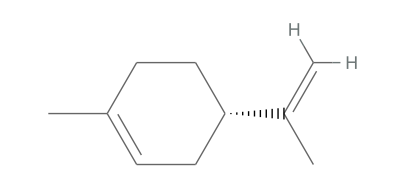
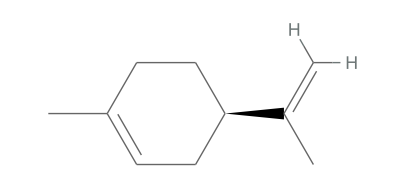
-Graphics3D- | -Graphics3D-
-Graphics- | -Graphics-
(-)-limonene | (+)-limonene | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics-
levopropoxyphene | propoxyphene
-Graphics3D- | -Graphics3D-
-Graphics- | -Graphics-
(R)-carvone | D-carvone | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics-
D-tartaric acid | L-tartaric acid

```mathematica
Grid[{{, }, {, }}]
```

Here, the (-) & (+), levo- & dextro-, (R)/(S) & (D)/(L) denote the chiral orientations of the molecules!

"D-tartaric acid" and "L-tartaric acid" are the molecules that "Louis Pasteur" first studied to observe chirality!  "(-)-limonene" comes from lemons, whereas "(+)-limonene" is found in oranges. "D-carvone" is from caraway seed oil, and "(R)-carvone" from spearmint oil. "levopropoxyphene" is known as Novrad and is an anti-cough agent, while "propoxyphene" is called Davron and is a painkiller.

You can see here that chirality is related to quite a great number of things:

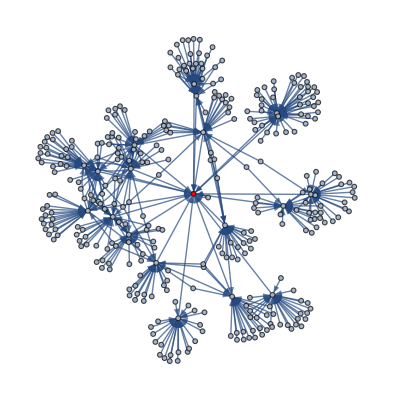

```mathematica
links=WikipediaData["Chirality","BacklinksRules","MaxLevelItems"->20,"MaxLevel"->2];
Graph[links,VertexLabels->Placed["Name",Tooltip],VertexStyle->{"Chirality"->Red}]
```

The coolest part about all of this, is that we can describe this mathematically. Give this a few glances:

## Hey! That looks like the DNA from up above, but it’s mathematical?

You’ve got that right! It is composed of the following, which can be descriptions of the mathematical functions that back left and right polarized light:

```mathematica
𝕩=Cos[# Pi/25]&/@Range@100;𝕩'=Cos[# Pi/25+Pi]&/@Range@100;
y=Cos[# Pi/25-Pi/2]&/@Range@100;y'=Cos[# Pi/25+Pi/2]&/@Range@100;
ldatcos={𝕩⟦#⟧,y⟦#⟧,#}&/@Range@100;
ldatchircos={𝕩'⟦#⟧,y⟦#⟧,#}&/@Range@100;
gchircos=Graphics3D[{{Thickness[0.03],Line[{#⟦1⟧,#⟦2⟧,#⟦3⟧}&/@ldatchircos]},
{Thickness[0.015],Green,Arrowheads[{0.015},Appearance->"Projected"],
Arrow[{1.5 #⟦1⟧,1.5 #⟦2⟧,#⟦3⟧}&/@ldatchircos⟦25;;75⟧]}},BoxRatios->{2,2,5},
AspectRatio->GoldenRatio,ImageSize->200,ViewAngle->Automatic,ViewCenter->{0.5,0.5,0.5},
ViewMatrix->Automatic,ViewPoint->{1.4000620728320412,0.013476838199693643,3.0805266704005962},
ViewProjection->Automatic,ViewRange->All,ViewVector->Automatic,
ViewVertical->{-0.8145880655494367,-0.004512056440937054,0.5800223485445198}];
gcos=Graphics3D[{{Thickness[0.03],Line[{#⟦1⟧,#⟦2⟧,#⟦3⟧}&/@ldatcos]},
{Thickness[0.015],Green,Arrowheads[{0.015},Appearance->"Projected"],
Arrow[{1.5 #⟦1⟧,1.5 #⟦2⟧,#⟦3⟧}&/@ldatcos⟦25;;75⟧]}},BoxRatios->{2,2,5},
AspectRatio->GoldenRatio,ImageSize->200,ViewAngle->Automatic,ViewCenter->{0.5,0.5,0.5},
ViewMatrix->Automatic,ViewPoint->{1.4000620728320412,0.013476838199693643,3.0805266704005962},
ViewProjection->Automatic,ViewRange->All,ViewVector->Automatic,
ViewVertical->{-0.8145880655494367,-0.004512056440937054,0.5800223485445198}];
Show[{gcos,gchircos}]
```

-Graphics3D-

## Wow. It all comes together, how amazing!

Yup! Thanks for chatting with me about Chirality!!

## Of course, and thank you for letting me in on such a beautiful secret that surrounds all of us!

Any time. Here’s one last fun example to take home with you:

```mathematica
Grid[{{Rasterize@Style["🐺",86], ImageReflect[Rasterize@Style["🐺",86],Left]}}]
```

-Graphics- | -Graphics-